```mathematica
<<Units`
<<PhysicalConstants`

T=300SI[Kelvin];
d=20 ;

Print["Thermodynamic β in terms of (eV):"]
β=(BoltzmannConstant T/SI[ElectronVolt])^-1
Print["Backbone spring constant (eV/Å^2) : "]
κ=0.1 
Print["κ/σ ratio:"]
κσr=125
Print["Base-pair spring constant (eV/Å^2) :"]
σ=κ/κσr
Print["e0 (eV):"]
ϵ=(σ d^2)/12
```

Thermodynamic β in terms of (eV):

38.6817

Backbone spring constant (eV/Å^2) :

0.1

κ/σ ratio:

125

Base-pair spring constant (eV/Å^2) :

0.0008

e0 (eV):

0.0266667

### Shikha Potential (2011)

The shikha potential in real dimensions is of the form

```mathematica
sV[η_]:=-ϵ/((1+(2 η^2)/d^2)^3)
```

Transforming the potential into dimensionless form we have

```mathematica
ShikhaβV[η_]:=-β/((1+(2 η^2)/d^2)^3)
```

```mathematica
ShikhaβV[0]//N
```

-38.6817

-38.6817

### Harmonic Approximation of the Shikha Potential (2011)

```mathematica
sVh[η_]:=-ϵ+1/2 σ η^2
```

The dimensionless form of v1 requires the dimenion transformation of the varaible η, and parameter d-has units of length.

```mathematica
ShikhaβVh[η_]:=-β +β(2 η^2)/κσr
```

```mathematica
ShikhaβVh[0]//N
```

-38.6817

-38.6817

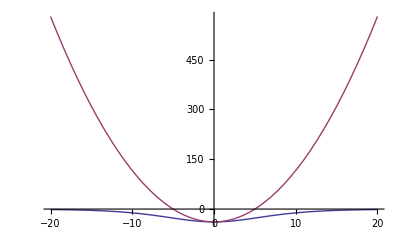

```mathematica
Plot[{ShikhaβV[x],ShikhaβVh[x]},{x,-20,20},PlotRange->Automatic,PlotStyle->{Thick},AxesOrigin->{0,0}]
```